```mathematica
Show[jupiterGraph,saturnGraph,uranusGraph,neptuneGraph,plutoGraph]
```

-Graphics3D-

```mathematica
timeConvert=1000;
```

```mathematica
(*Jupiter*)
jupSemiMajor=QuantityMagnitude[jupiterSemiMajorAxis,"Meters"];
jupSemiMinor = QuantityMagnitude[jupiterSemiMinorAxis,"Meters"];
paraJupx [t_]= jupSemiMajor*Cos[t*timeConvert/jupiterOrbitEarthYears];
paraJupy[t_]=jupSemiMinor*Sin[t*timeConvert/jupiterOrbitEarthYears];
jupParaPair = {paraJupx[t],paraJupy[t]};
jupPlot2D=ParametricPlot[jupParaPair,{t,0,5Pi}];
```

```mathematica
(*Saturn*)
```

```mathematica
satSemiMajor=QuantityMagnitude[saturnSemiMajorAxis,"Meters"];
satSemiMinor = QuantityMagnitude[saturnSemiMinorAxis,"Meters"];
paraSatx [t_]= satSemiMajor*Cos[t*timeConvert/saturnOrbitEarthYears];
paraSaty[t_]=satSemiMinor*Sin[t*timeConvert/saturnOrbitEarthYears];
satParaPair={paraSatx[t],paraSaty[t]};
satPlot2D=ParametricPlot[satParaPair,{t,0,5Pi}];
```

```mathematica
(*Uranus*)
```

```mathematica
uraSemiMajor=QuantityMagnitude[uranusSemiMajorAxis,"Meters"];
uraSemiMinor = QuantityMagnitude[uranusSemiMinorAxis,"Meters"];
paraUrax [t_]= uraSemiMajor*Cos[t*timeConvert/uranusOrbitEarthYears];
paraUray[t_]= uraSemiMinor*Sin[t*timeConvert/uranusOrbitEarthYears];
uraParaPair={paraUrax[t],paraUray[t]};
uraPlot2D=ParametricPlot[uraParaPair,{t,0,5Pi}];
```

```mathematica
(*Neptune*)
```

```mathematica
nepSemiMajor=QuantityMagnitude[neptuneSemiMajorAxis,"Meters"];
nepSemiMinor = QuantityMagnitude[neptuneSemiMinorAxis,"Meters"];
paraNepx [t_]= nepSemiMajor*Cos[t*timeConvert/neptuneOrbitEarthYears];
paraNepy[t_]=nepSemiMinor*Sin[t*timeConvert/neptuneOrbitEarthYears];
nepParaPair={paraNepx[t],paraNepy[t]};
nepPlot2D=ParametricPlot[nepParaPair,{t,0,5Pi}];
```

```mathematica
(*Pluto*)
```

```mathematica
pluSemiMajor=QuantityMagnitude[plutoSemiMajorAxis,"Meters"];
pluSemiMinor = QuantityMagnitude[plutoSemiMinorAxis,"Meters"];
paraPlux [t_]= pluSemiMajor*Cos[t*timeConvert/plutoOrbitEarthYears];
paraPluy[t_]=pluSemiMinor*Sin[t*timeConvert/plutoOrbitEarthYears];
pluParaPair={paraPlux[t],paraPluy[t]};
pluPlot2D=ParametricPlot[pluParaPair,{t,0,5Pi}];
```

```mathematica
outerPlanet2DParametrics={jupParaPair,satParaPair,uraParaPair,nepParaPair,pluParaPair};
```

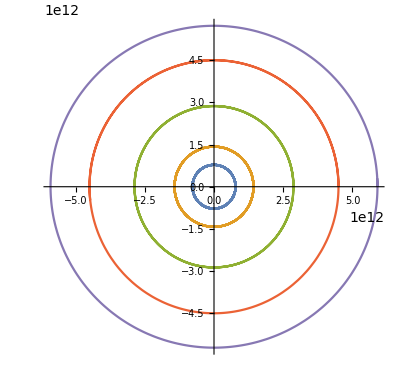

```mathematica
outerPlanet2DParaPlot=ParametricPlot[outerPlanet2DParametrics,{t,0,5Pi},PlotRange->All]
```

```mathematica
Animate[Show[outerPlanet2DParaPlot,Graphics[{PointSize[Large],Point[{paraJupx[t],paraJupy[t]}],Point[{paraSatx[t],paraSaty[t]}],Point[{paraUrax[t],paraUray[t]}],Point[{paraNepx[t],paraNepy[t]}],Point[{paraPlux[t],paraPluy[t]}]}]],{t,0,2Pi}]
(* PUT ALL TIMING AS RATIOS OF EARTH YEARS*)
```